# χ_4

### load data

### data loading

```mathematica
p0s={3.85,3.825,3.80,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{ 1,1,1,1,1,60, 80, 200, 500, 800, 999999, 999999, 999999,999999, 999999, 999999, 999999},{ 1,1,1,1,1,25, 40 ,60, 80, 120,200 ,300 ,1000 ,999999, 999999,999999},{1,1,1,1,1,40 ,70 ,150 ,250, 600 ,2000, 999999 ,999999, 999999},{1,1,1,10 ,30 ,70, 150 ,700,1400, 999999 ,999999}};
```

```mathematica
CRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]
],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
(*get the CRSISF with the same time steps*)
```

```mathematica
missingParts={{3,1,5},{3,1,6},{3,1,8},{3,2,6},{3,2,8},{3,3,7},{3,4,6},{3,4,7},{3,4,8},{3,5,5},{3,5,7},{3,5,8},{3,6,6},{3,6,7},{3,6,8},{3,7,5},{3,7,6},{3,7,7},{3,8,5},{3,8,6},{3,8,8},{3,9,5},{3,9,6},{3,9,7},{3,10,6},{3,10,7},{3,11,5},{4,1,7},{4,2,10},{4,3,10},{4,4,7},{4,4,8},{4,4,9},{4,4,10},{4,5,9},{4,6,6},{4,6,8},{4,6,10},{4,7,8},{4,7,9},{4,8,9},{4,8,10},{4,9,10}};
```

```mathematica
tauEstimateMissning={1,1,1,3,3,4,8,8,8,15,15,15,40,40,40,70,70,70,150,150,150,250,250,250,600,600,2000,4,5,7,10,10,10,10,30,70,70,70,150,150,700,700,1400};
```

```mathematica
p0s[[missingParts[[57,1]]]]
```

3.75

```mathematica
i
```

58

```mathematica
For[i=1,i<=Length[missingParts],i++,CRSISF[[missingParts[[i,1]],missingParts[[i,2]],missingParts[[i,3]]]]=Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRSISF_MissingTrajectory_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[missingParts[[i,1]]]],p0s[[missingParts[[i,1]]]],temperatures[[missingParts[[i,1]],missingParts[[i,2]]]],Floor[If[tauEstimateMissning[[i]]==999999,tauEstimateMissning[[i]],If[tauEstimateMissning[[i]]<1000,10000,tauEstimateMissning[[i]]*10]]
],records[[missingParts[[i,1]],missingParts[[i,3]]]]},{3,4,8,0,0}],"Data"]]
```

```mathematica
timeVar=Table[Table[Table[Variance[Table[CRSISF[[p,T,i,1,rec]]-CRSISF[[p,T,i,1,1]],{i,Length[records[[p]]]}]],{rec,Min[Table[Length[CRSISF[[p,T,i,1]]],{i,Length[records[[p]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
chi4=Table[Table[Table[4096*Variance[Table[CRSISF[[p,T,i,2,rec]],{i,Length[records[[p]]]}]],{rec,Min[Table[Length[CRSISF[[p,T,i,1]]],{i,Length[records[[p]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Table[Table[Table[Length[CRSISF[[p,T,i,1]]],{i,10}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{639,640,640,640,640,637,639,639,639,639},{639,640,640,640,640,639,638,639,639,639},{639,640,640,640,640,639,639,639,639,639},{640,640,640,640,640,639,639,639,639,639},{640,640,640,640,640,639,639,639,639,639},{640,640,640,640,640,639,639,639,638,639},{640,640,640,640,640,639,639,639,639,639}},{{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{641,641,641,641,641,639,637,640,641,641},{641,640,641,641,641,640,639,639,641,641},{641,641,641,641,641,641,639,640,640,641}},{{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{117,117,113,114,117,117,117,117,117,117},{580,580,580,580,589,640,641,641,640,640},{580,580,580,580,580,590,641,641,640,640},{641,580,580,580,641,640,641,641,640,641}},{{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{111,111,111,111,111,111,111,111,111,111},{113,113,113,113,113,113,113,113,113,113},{568,569,567,568,568,569,569,569,569,568},{569,569,568,569,569,569,569,568,569,568}}}

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/missingTrajectory_N4096_p3.8000_T0.00310000_idx14.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/postion→NumericArray[<117,8192>, Real64],/time→NumericArray[…]|>

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeCRSISF_MissingTrajectory_N4096_p3.8000_T0.00310000_waitingTime20000_idx14.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
timeVar[[1,1,1]]
```

0.

```mathematica
Length[CRSISF[[1,1,1,1]]]
```

380

```mathematica
Table[Table[{CRSISF[[1,T,1,1,rec]]-CRSISF[[1,T,1,1,1]],chi4[[1,T,rec]]},{rec,Min[Table[Length[CRSISF[[1,T,copy,1]]],{copy,10}]]}],{T,Length[temperatures[[1]]]}]
```

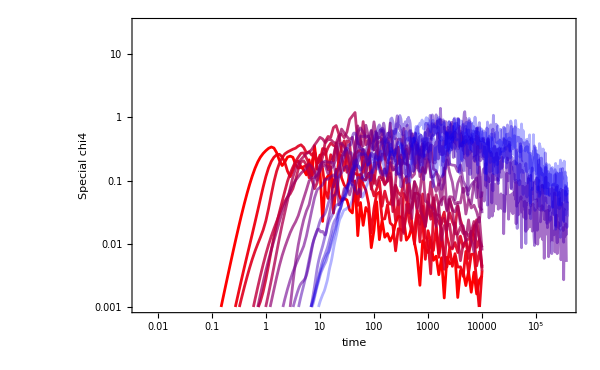
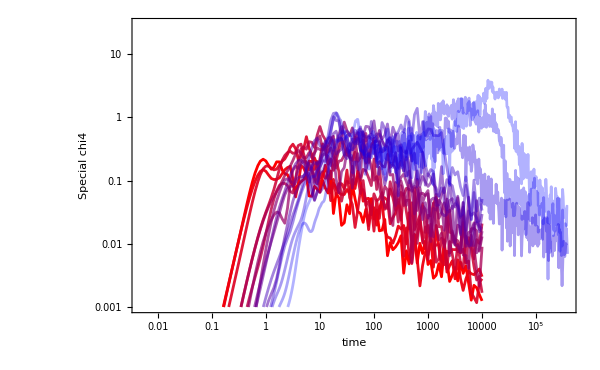
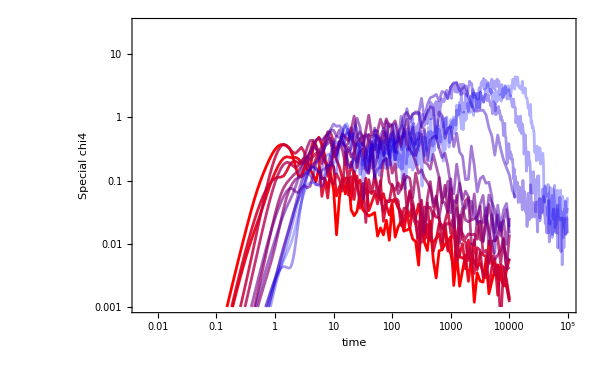
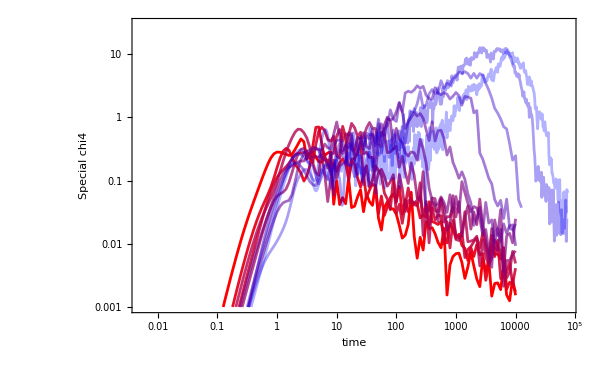

```mathematica
Table[ListLogLogPlot[Table[Table[{CRSISF[[p,T,1,1,rec]]-CRSISF[[p,T,1,1,1]],chi4[[p,T,rec]]},{rec,1,Min[Table[Length[CRSISF[[p,T,copy,1]]],{copy,10}]]}],{T,Length[temperatures[[p]]]}],FrameLabel->{"time","Special chi4"},ImageSize->600,PlotRange->{All,{0.001,30}},PlotLabel->"",Joined->True,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]]],{p,Length[p0s]}]
```

```mathematica
chi4Table=Table[Table[Prepend[Table[{CRSISF[[p,T,1,1,rec]]-CRSISF[[p,T,1,1,1]],chi4[[p,T,rec]]},{rec,1,Min[Table[Length[CRSISF[[p,T,copy,1]]],{copy,10}]]}],{"time","chi4"}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Table[Table[Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p"<>ToString[NumberForm[p0s[[p]],{5,3}]]<>"_T"<>ToString[NumberForm[temperatures[[p,T]],{8,8}]]<>".csv",chi4Table[[p,T]],"CSV"],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.03900000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.01600000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.01000000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00500000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00385000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00250000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00200000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00100000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00050000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00033000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00025000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00014000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00009100.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00007700.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00005400.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00004500.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.850_T0.00003600.csv},{/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.06300000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.03900000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.03105000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.01600000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.01000000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00800000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00630000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00500000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00385000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00310000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00250000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00200000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00150000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00100000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00067000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.825_T0.00050000.csv},{/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.06300000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.03900000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.03105000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.02500000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.01600000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.01000000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.00800000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.00630000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.00500000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.00385000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.00310000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.00280000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.00250000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.800_T0.00220000.csv},{/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.06300000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.03900000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.03105000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.02500000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.02000000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.01600000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.01400000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.01200000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.01100000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.01000000.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/chi4/chi4_p3.750_T0.00930000.csv}}